```mathematica
Clear["Global`*"]
```

## Geometric picture of evolution of k-fermion modes - AD protocol - Pi/4

#### no noise,

```mathematica
uk = Import["/home/yajur/Dropbox/miniproj/outputs/uk_100spins_200kicks.dat"];
vk = Import["/home/yajur/Dropbox/miniproj/outputs/vk_100spins_200kicks.dat"];
ukhalf=N[Flatten@ToExpression@StringSplit[uk[[1]],","]];
vkhalf=N[Flatten@ToExpression@StringSplit[vk[[1]],","]];
```

```mathematica
vkhalf
```

{0.0157073,0.0471065,0.0784591,0.109734,0.140901,0.171929,0.202787,0.233445,0.263873,0.29404,0.323917,0.353475,0.382683,0.411514,0.439939,0.46793,0.495459,0.522499,0.549023,0.575005,0.60042,0.625243,0.649448,0.673013,0.695913,0.718126,0.739631,0.760406,0.78043,0.799685,0.81815,0.835807,0.85264,0.868632,0.883766,0.898028,0.911403,0.92388,0.935444,0.946085,0.955793,0.964557,0.97237,0.979223,0.985109,0.990024,0.993961,0.996917,0.99889,0.999877,0.999877,0.99889,0.996917,0.993961,0.990024,0.985109,0.979223,0.97237,0.964557,0.955793,0.946085,0.935444,0.92388,0.911403,0.898028,0.883766,0.868632,0.85264,0.835807,0.81815,0.799685,0.78043,0.760406,0.739631,0.718126,0.695913,0.673013,0.649448,0.625243,0.60042,0.575005,0.549023,0.522499,0.495459,0.46793,0.439939,0.411514,0.382683,0.353475,0.323917,0.29404,0.263873,0.233445,0.202787,0.171929,0.140901,0.109734,0.0784591,0.0471065,0.0157073,-0.0157073,-0.0471065,-0.0784591,-0.109734,-0.140901,-0.171929,-0.202787,-0.233445,-0.263873,-0.29404,-0.323917,-0.353475,-0.382683,-0.411514,-0.439939,-0.46793,-0.495459,-0.522499,-0.549023,-0.575005,-0.60042,-0.625243,-0.649448,-0.673013,-0.695913,-0.718126,-0.739631,-0.760406,-0.78043,-0.799685,-0.81815,-0.835807,-0.85264,-0.868632,-0.883766,-0.898028,-0.911403,-0.92388,-0.935444,-0.946085,-0.955793,-0.964557,-0.97237,-0.979223,-0.985109,-0.990024,-0.993961,-0.996917,-0.99889,-0.999877,-0.999877,-0.99889,-0.996917,-0.993961,-0.990024,-0.985109,-0.979223,-0.97237,-0.964557,-0.955793,-0.946085,-0.935444,-0.92388,-0.911403,-0.898028,-0.883766,-0.868632,-0.85264,-0.835807,-0.81815,-0.799685,-0.78043,-0.760406,-0.739631,-0.718126,-0.695913,-0.673013,-0.649448,-0.625243,-0.60042,-0.575005,-0.549023,-0.522499,-0.495459,-0.46793,-0.439939,-0.411514,-0.382683,-0.353475,-0.323917,-0.29404,-0.263873,-0.233445,-0.202787,-0.171929,-0.140901,-0.109734,-0.0784591,-0.0471065,-0.0157073}

```mathematica
theta = ArcCos[ukhalf];
```

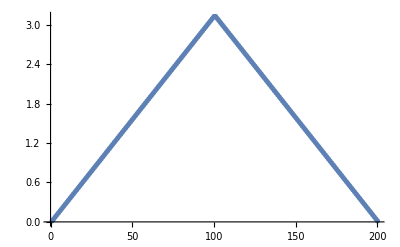

```mathematica
ListPlot[theta]
```

#### with noise - system size = 100. So there are 50 uks and vks.

```mathematica
uknoise = Import["/home/yajur/Dropbox/miniproj/outputs/uk_noise100spins_2000kicks.dat"];
vknoise = Import["/home/yajur/Dropbox/miniproj/outputs/vk_noise100spins_2000kicks.dat"];
uknoisee = N[Flatten@ToExpression@StringSplit[Flatten[uknoise],","]];
vknoisee  =N[Flatten@ToExpression@StringSplit[Flatten[vknoise],","]];
```

```mathematica
uknoiseall = Table[Table[uknoisee[[i]],{i,2000*(j-1)+1,2000*j}],{j,1,50}];
vknoiseall = Table[Table[vknoisee[[i]],{i,2000*(j-1)+1,2000*j}],{j,1,50}];
```

```mathematica
cSpherical[θ_,ϕ_] := {1, θ, ϕ}
```

```mathematica
cCartesian = Table[Table[Re[CoordinateTransform["Spherical"->"Cartesian",cSpherical[2ArcCos[Abs[vknoiseall[[i,j]]]],Arg[(uknoiseall[[i,j]]/vknoiseall[[i,j]]) Cot[ArcCos[Abs[vknoiseall[[i,j]]]]]]]]],{j,1,2000}],{i,1,1}];
```

```mathematica
Dimensions[cCartesian[[5,1]]]
```

{3}

```mathematica
cCartesian[[3,1]]
```

{0.156434,0.,-0.987688}

```mathematica
Manipulate[Show[Graphics3D[{Opacity[.25],Sphere[]}],ListPointPlot3D[{cCartesian[[1,k]]},PlotStyle->Blue],Graphics3D[{Blue,Arrow[{{0,0,0},cCartesian[[1,1]]}],Text["|1/2>",{{0,0,-1.1},{0,0,0}}]}],Graphics3D[{Thick,Arrow[{{0,0,0},{0,0,1}}],Text["|0>",{{0,0,1.1},{0,0,0}}]}],Graphics3D[{Gray,Arrowheads[Small],Arrow[{{0,0,0},{0,-1,0}}]}],Graphics3D[{{Gray,Thick},Arrow[{{0,0,0},{1,0,0}}],Text["|+>",{{1.1,0,0},{0,0,0}}]}],Boxed->False],{k,1,2000,1}]
```

```mathematica
Show[Graphics3D[{Opacity[.25],Sphere[]},Axes->True],Table[{ParametricPlot3D[cCartesian[t,k Pi/30],{t,0,Pi},PlotStyle->Thick,ColorFunction->(Hue[1#4]&)],Graphics3D[{Red,Arrow[{{0,0,0},{0,-Sin[k Pi/6],-Cos[k Pi/6]}}]},Axes->True]},{k,1,29}],Graphics3D[{Thick,Arrow[{{0,0,0},{0,0,-1}}]},Axes->True]]
```

-Graphics3D-

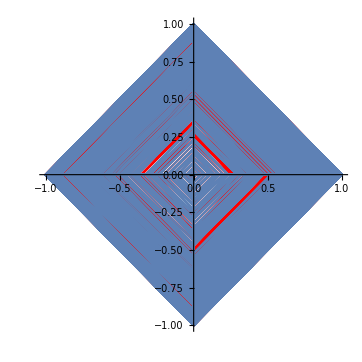

```mathematica
Show[ListLinePlot[(Tooltip[{Re[#1],Im[#1]}]&)/@vknoiseall[[5]],AspectRatio->1,PlotRange->All,PlotStyle->Red],
ListLinePlot[(Tooltip[{Re[#1],Im[#1]}]&)/@uknoiseall[[5]],AspectRatio->1,PlotRange->All]]
```

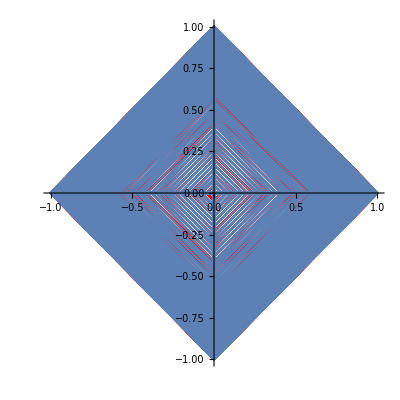

```mathematica
Show[ListLinePlot[(Tooltip[{Re[#1],Im[#1]}]&)/@vknoise3half,AspectRatio->1,PlotRange->All,PlotStyle->Red],
ListLinePlot[(Tooltip[{Re[#1],Im[#1]}]&)/@uknoise3half,AspectRatio->1,PlotRange->All]]
```

```mathematica
xycoord = Table[{Sin[thetanoisehalf][[i]],0,Cos[thetanoisehalf][[i]]},{i,1,2000}];
```

```mathematica
uknoisehalf
```

{0.999877+0. ⅈ,0.+0.999877 ⅈ,-0.999877+0. ⅈ,0.-0.999877 ⅈ,0.999877+0. ⅈ,0.+0.999877 ⅈ,-0.999877+0. ⅈ,0.-0.999877 ⅈ,0.999877+0. ⅈ,1982,0.+0.883766 ⅈ,0.+0.85264 ⅈ,-0.85264+0. ⅈ,0.-0.85264 ⅈ,0.85264+0. ⅈ,0.883766+0. ⅈ,0.+0.883766 ⅈ,0.+0.85264 ⅈ,-0.85264+0. ⅈ}
 |  |  |  |

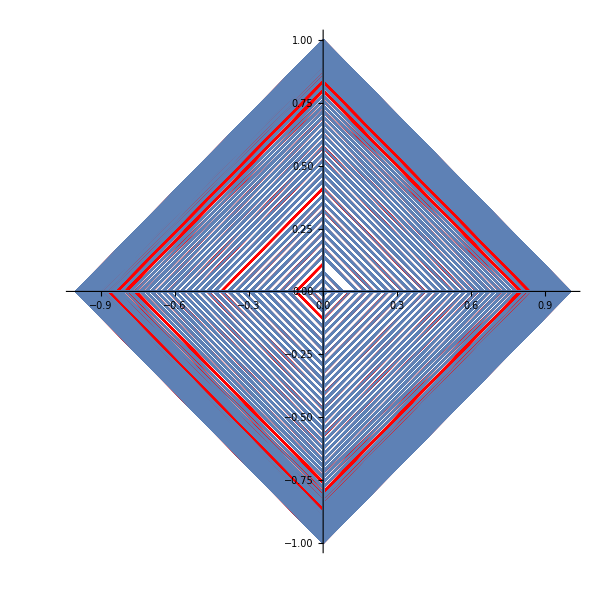

```mathematica
Show[ListLinePlot[(Tooltip[{Re[#1],Im[#1]}]&)/@vknoisehalf,AspectRatio->1,PlotRange->All,PlotStyle->Red],
ListLinePlot[(Tooltip[{Re[#1],Im[#1]}]&)/@uknoisehalf,AspectRatio->1,PlotRange->All]]
```

```mathematica
(*Manipulate[Show[Graphics3D[{Opacity[.25],Sphere[]},Axes->True],ListPointPlot3D[Table[xycoord[[p]],{p,1,t}]]],{t,1,2000,5}]*)
```

## Same as above T = Pi/4 + 0.01

```mathematica
uknoise01 = N[Flatten@ToExpression@StringSplit[Flatten[Import["/home/yajur/Dropbox/miniproj/outputs/ADprotocol/job2340067/uk_100_piby4plus0001_2000kicks.dat"]],","]]

vknoise01 = N[Flatten@ToExpression@StringSplit[Flatten[Import["/home/yajur/Dropbox/miniproj/outputs/ADprotocol/job2340067/vk_100_piby4plus0001_2000kicks.dat"]],","]]
```

{0.999877+0. ⅈ,0.99889+0. ⅈ,0.996919+0. ⅈ,0.993963+0. ⅈ,-0.0198188+0.996719 ⅈ,-0.0197402+0.99869 ⅈ,99988,-0.209703-0.401714 ⅈ,0.199036+0.401965 ⅈ,0.389479-0.233772 ⅈ,-0.214614-0.392615 ⅈ,0.202737+0.390138 ⅈ,0.380135-0.238028 ⅈ}
 |  |  |  |

{0.0157073+0. ⅈ,0.0470939-0.000628125 ⅈ,0.078434-0.00125563 ⅈ,0.109697-0.0018819 ⅈ,-0.00407438-0.0783682 ⅈ,-0.00406943-0.0470218 ⅈ,99989,-0.854503+0.261981 ⅈ,-0.257334-0.852899 ⅈ,0.864795-0.227867 ⅈ,-0.879772+0.180806 ⅈ,-0.175338-0.876411 ⅈ}
 |  |  |  |

```mathematica
uknoiseall01 = Table[Table[uknoise01[[i]],{i,2000*(j-1)+1,2000*j}],{j,1,50}];
vknoiseall01 = Table[Table[vknoise01[[i]],{i,2000*(j-1)+1,2000*j}],{j,1,50}];
```

```mathematica
cSpherical[θ_,ϕ_] := {1, θ, ϕ}
```

```mathematica
cCartesian01 = Table[Re[CoordinateTransform["Spherical"->"Cartesian",cSpherical[2ArcCos[Abs[vknoiseall01[[1,j]]]],Arg[(uknoiseall01[[1,j]]/vknoiseall01[[1,j]]) Cot[ArcCos[Abs[vknoiseall01[[1,j]]]]]]]]],{j,1,2000}];
```

```mathematica
cCartesian012 = Table[Re[CoordinateTransform["Spherical"->"Cartesian",cSpherical[2ArcCos[Abs[vknoiseall01[[2,j]]]],Arg[(uknoiseall01[[2,j]]/vknoiseall01[[2,j]]) Cot[ArcCos[Abs[vknoiseall01[[2,j]]]]]]]]],{j,1,2000}];
```

```mathematica
cCartesian013 = Table[Re[CoordinateTransform["Spherical"->"Cartesian",cSpherical[2ArcCos[Abs[vknoiseall01[[3,j]]]],Arg[(uknoiseall01[[3,j]]/vknoiseall01[[3,j]]) Cot[ArcCos[Abs[vknoiseall01[[3,j]]]]]]]]],{j,1,2000}];
```

```mathematica
Show[Graphics3D[{Opacity[.25],Sphere[]},Axes->True],ListPointPlot3D[cCartesian,PlotStyle->Blue],ListPointPlot3D[cCartesian01,PlotStyle->Purple],ListPointPlot3D[cCartesian013,PlotStyle->Red]]
```

-Graphics3D-

```mathematica
Manipulate[Show[Graphics3D[{Opacity[.25],Sphere[]}],Graphics3D[{Thick,Arrow[{{0,0,0},{0,0,1}}],Text["|0>",{{0,0,1.1},{0,0,0}}]}],Graphics3D[{{Gray,Thick},Arrow[{{0,0,0},{1,0,0}}],Text["|+>",{{1.1,0,0},{0,0,0}}]}],Graphics3D[{Gray,Arrowheads[Small],Arrow[{{0,0,0},{0,1,0}}]}],ListPointPlot3D[Table[cCartesian01[[i]],{i,1,k}],PlotStyle->Red],Boxed->False],{k,1,2000}]
```

```mathematica
Show[Graphics3D[{Opacity[.25],Sphere[]}],ListPointPlot3D[cCartesian[[3]],PlotStyle->Black],Graphics3D[{{Thick,Blue},Arrow[{{0,0,0},cCartesian[[3,1]]}],Text["|5/2>",{{0.24,0.,-1.09},{0,0,0}}]}],Graphics3D[{Thick,Arrow[{{0,0,0},{0,0,1}}],Text["|0>",{{0,0,1.1},{0,0,0}}]}],Graphics3D[{{Gray,Thick},Arrow[{{0,0,0},{1,0,0}}],Text["|+>",{{1.1,0,0},{0,0,0}}]}],ListPointPlot3D[cCartesian013,PlotStyle->Red],Boxed->False]
```

-Graphics3D-

```mathematica
Show[Graphics3D[{Opacity[.25],Sphere[]},Axes->True],ListPointPlot3D[cCartesian,PlotStyle->Blue],ListPointPlot3D[cCartesian01,PlotStyle->Green]]
```

-Graphics3D-

```mathematica
(*Manipulate[Show[Graphics3D[{Opacity[.25],Sphere[]},Axes->True],ListPointPlot3D[Table[cCartesian01[[i]],{i,1,k}],ColorFunction->"Rainbow"]],{k,1,2000,1}]*)
```

## Same as above T = Pi/4 + 0.001

```mathematica
uknoise01 = N[Flatten@ToExpression@StringSplit[Flatten[Import["/home/yajur/Dropbox/miniproj/outputs/ADprotocol/job2339858/uk_100_50_piby4plus01.dat"]],","]]

vknoise01 = N[Flatten@ToExpression@StringSplit[Flatten[Import["/home/yajur/Dropbox/miniproj/outputs/ADprotocol/job2339858/vk_100_50_piby4plus01.dat"]],","]]
```

{0.999877+0. ⅈ,0.99889+0. ⅈ,0.996919+0. ⅈ,-0.0198976+0.99869 ⅈ,-0.996123-0.039945 ⅈ,-0.99317-0.0399844 ⅈ,9988,-0.356961+0.244691 ⅈ,0.357441-0.232445 ⅈ,-0.356996+0.219597 ⅈ,0.253825+0.343937 ⅈ,-0.294581-0.325669 ⅈ,-0.32701+0.273679 ⅈ}
 |  |  |  |

{0.0157073+0. ⅈ,0.0470939-0.000628125 ⅈ,0.078434-0.00125563 ⅈ,-0.00282334-0.0470468 ⅈ,-0.0783211+0.00313738 ⅈ,9990,0.313499+0.848483 ⅈ,-0.268095-0.867442 ⅈ,0.865306-0.261773 ⅈ,-0.866467+0.237479 ⅈ,-0.209759-0.879867 ⅈ}
 |  |  |  |

```mathematica
uknoiseall01 = Table[Table[uknoise01[[i]],{i,200*(j-1)+1,200*j}],{j,1,50}];
vknoiseall01 = Table[Table[vknoise01[[i]],{i,200*(j-1)+1,200*j}],{j,1,50}];
```

```mathematica
cSpherical[θ_,ϕ_] := {1, θ, ϕ}
```

```mathematica
cCartesian01 = Table[Re[CoordinateTransform["Spherical"->"Cartesian",cSpherical[2ArcCos[Abs[vknoiseall01[[1,j]]]],Arg[(uknoiseall01[[1,j]]/vknoiseall01[[1,j]]) Cot[ArcCos[Abs[vknoiseall01[[1,j]]]]]]]]],{j,1,200}];
```

```mathematica
Show[Graphics3D[{Opacity[.25],Sphere[]},Axes->True],ListPointPlot3D[cCartesian01,PlotStyle->Thick]]
```

-Graphics3D-

## A.SenD.sen Protocol

```mathematica
senuknoise = Import["/home/yajur/Dropbox/miniproj/outputs/senuk_noise100spins_2000kicks.dat"];
```

```mathematica
senvknoise = Import["/home/yajur/Dropbox/miniproj/outputs/senvk_noise100spins_2000kicks.dat"];
```

```mathematica
senuknoisee = N[Flatten@ToExpression@StringSplit[Flatten[senuknoise],","]];
```

```mathematica
senvknoisee  =N[Flatten@ToExpression@StringSplit[Flatten[senvknoise],","]];
```

```mathematica
Dimensions[uknoise]
```

{50,2000}

```mathematica
Dimensions[senuknoisee]
```

{100000}

```mathematica
senvknoisee
```

{0.+0. ⅈ,-0.0145776-0.113415 ⅈ,-0.0253849-0.197497 ⅈ,-0.0385791-0.234182 ⅈ,-0.0219051-0.234586 ⅈ,-0.000673864-0.186185 ⅈ,99988,0.0298643+0.164888 ⅈ,0.0339539+0.141121 ⅈ,0.0196983+0.0699402 ⅈ,-0.00786121-0.059266 ⅈ,-0.0238558-0.147511 ⅈ,-0.0401812-0.142827 ⅈ}
 |  |  |  |

```mathematica
senuknoiseall = Table[Table[senuknoisee[[i]],{i,2000*(j-1)+1,2000*j}],{j,1,50}];
```

```mathematica
senvknoiseall = Table[Table[senvknoisee[[i]],{i,2000*(j-1)+1,2000*j}],{j,1,50}];
```

## geometry

```mathematica
xy = Table[{1,0},{i,1,50}];
```

```mathematica
B[k_] = {{Cos[Pi (2k-1)/100],Sin[Pi (2k-1)/100]},{-Sin[Pi (2k-1)/100],Cos[Pi (2k-1)/100]}}
```

{{Cos[1/100 (-1+2 k) π],Sin[1/100 (-1+2 k) π]},{-Sin[1/100 (-1+2 k) π],Cos[1/100 (-1+2 k) π]}}

```mathematica
A[k_] = B[k].PauliMatrix[3]
```

{{Cos[1/100 (-1+2 k) π],-Sin[1/100 (-1+2 k) π]},{-Sin[1/100 (-1+2 k) π],-Cos[1/100 (-1+2 k) π]}}

```mathematica
xy1= Table[A[i].B[i].xy[[i]],{i,1,50}];
```

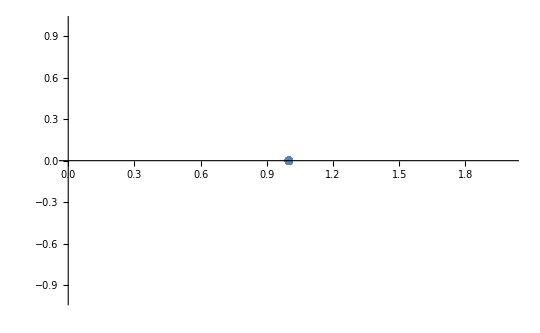

```mathematica
ListPlot[xy1]
```

## Eigen spectrum of reduced density matrix